# Лабораторная работа №5 Интерполирование 1.1.2(в)

Выполнил:Сайков Константин
																				Группа: ПМ1801

```mathematica
PolEx[n_,x_]:=
a0+Sum[ToExpression[StringJoin[ToString[a],ToString[i]]]*ⅇ^(i*x)+ToExpression[StringJoin[ToString[b],ToString[i]]]*ⅇ^(-i*x),{i,1,n}]
```

```mathematica
PolEx2[exp_,y_]:=exp==y
```

```mathematica
mainF[n_,x_,y_]:=Module[{sys,element,res,first},
element = Join[{a0},Table[ToExpression[StringJoin[ToString[a],ToString[i]]],{i,1,n}],Table[ToExpression[StringJoin[ToString[b],ToString[i]]],{i,1,n}]
];
sys= Map[PolEx[n,#]&,x];
sys=Table[PolEx2[sys[[i]],y[[i]]],{i,1,Length@y}];
res = NSolve[sys,element];
first = res[[1,1,2]];
res = Drop[res[[1]],1];
first+Sum[ⅇ^(k*x1)res[[k,2]]+ⅇ^(-k*x1)res[[n+k,2]],{k,1,n}]
]
```

1.Пишем функцию
2.Выбираем точки по х
3.При помощи этой же функции генерируем точки по y
4. Запускаем и сверяем результат
Формула
-Graphics-

Тест №1
Полином

```mathematica
f[x_]:= x^3-3 x^2
```

```mathematica
f/@{0,2,3,5,6}
```

{0,-4,0,50,108}

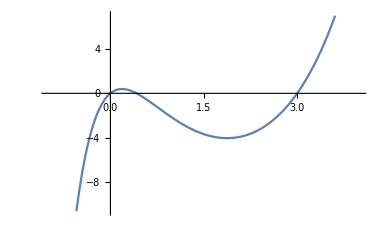

```mathematica
Plot[mainF[2,{0,2,3,5,6},{0,-4,0,50,108}],{x1,-1,4}]
```

Тест №2
Тригонометрическая функция

```mathematica
f[x_]:= Sin[x]
```

```mathematica
f/@{0,Pi/6,Pi/3,Pi/2,Pi,(7Pi)/6,(4Pi)/3}
```

{0,1/2,(√3)/2,1,0,-1/2,-(√3)/2}

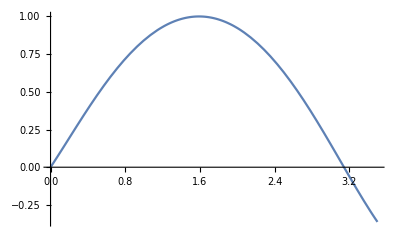

```mathematica
Plot[mainF[3,{0,Pi/6,Pi/3,Pi/2,Pi,(7Pi)/6,(4Pi)/3},{0,1/2,(√3)/2,1,0,-1/2,-(√3)/2}],{x1,0,3.5}]
```

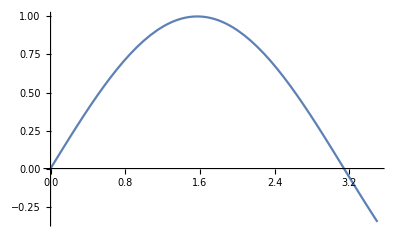

```mathematica
Plot[ Sin[x],{x,0,3.5}]
```

Тест №3

```mathematica
f[x_]:= Sin[x]+Cos[x]
```

```mathematica
f/@{0,Pi/6,Pi/3,Pi/2,Pi,(7Pi)/6,(4Pi)/3}
```

{1,1/2+(√3)/2,1/2+(√3)/2,1,-1,-1/2-(√3)/2,-1/2-(√3)/2}

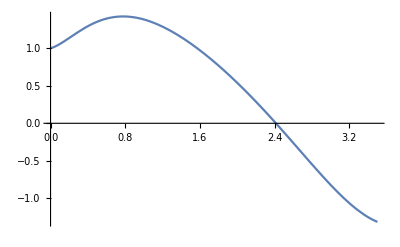

```mathematica
Plot[mainF[3,{0,Pi/6,Pi/3,Pi/2,Pi,(7Pi)/6,(4Pi)/3},{1,1/2+(√3)/2,1/2+(√3)/2,1,-1,-1/2-(√3)/2,-1/2-(√3)/2}],{x1,0,3.5}]
```

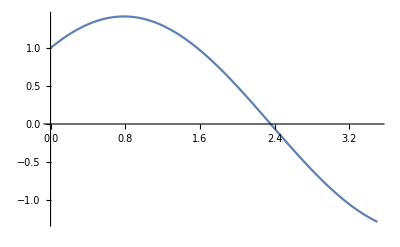

```mathematica
Plot[ Sin[x]+Cos[x],{x,0,3.5}]
```

Тест №4

```mathematica
f[x_]:=ⅇ^x+Cos[x]
```

```mathematica
f/@{0,Pi/6,Pi/3,Pi/2,Pi,(7Pi)/6,(4Pi)/3}
```

{2,(√3)/2+ⅇ^(π/6),1/2+ⅇ^(π/3),ⅇ^(π/2),-1+ⅇ^π,-(√3)/2+ⅇ^(7 π/6),-1/2+ⅇ^(4 π/3)}

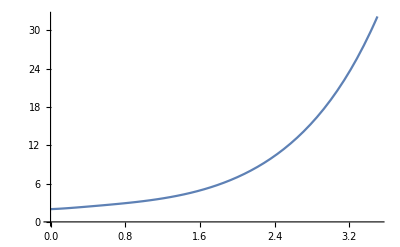

```mathematica
Plot[mainF[3,{0,Pi/6,Pi/3,Pi/2,Pi,(7Pi)/6,(4Pi)/3},{2,(√3)/2+ⅇ^(π/6),1/2+ⅇ^(π/3),ⅇ^(π/2),-1+ⅇ^π,-(√3)/2+ⅇ^(7 π/6),-1/2+ⅇ^(4 π/3)}],{x1,0,3.5}]
```

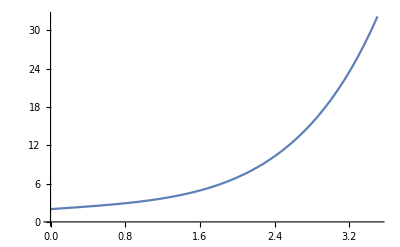

```mathematica
Plot[ ⅇ^x+Cos[x],{x,0,3.5}]
```

Теперь на места экспонент поставим гиперболический синус и гиперболически косинус
-Graphics-

```mathematica
PolTrig[n_,x_]:=
a0+Sum[ToExpression[StringJoin[ToString[a],ToString[i]]]*Cosh[i*x]+ToExpression[StringJoin[ToString[b],ToString[i]]]*Sinh[i*x],{i,1,n}]
```

```mathematica
mainF1[n_,x_,y_]:=Module[{sys,element,res,first},
element = Join[{a0},Table[ToExpression[StringJoin[ToString[a],ToString[i]]],{i,1,n}],Table[ToExpression[StringJoin[ToString[b],ToString[i]]],{i,1,n}]
];
sys= Map[PolTrig[n,#]&,x];
sys=Table[PolEx2[sys[[i]],y[[i]]],{i,1,Length@y}];
res = NSolve[sys,element];
first = res[[1,1,2]];
res = Drop[res[[1]],1];
first+Sum[Cosh[k*x1]res[[k,2]]+Sinh[k*x1]res[[n+k,2]],{k,1,n}]
]
```

Тест №1

```mathematica
f[x_]:=ⅇ^x
```

```mathematica
f/@{-2,0,2,4,6,8,10}
```

{1/ⅇ^2,1,ⅇ^2,ⅇ^4,ⅇ^6,ⅇ^8,ⅇ^10}

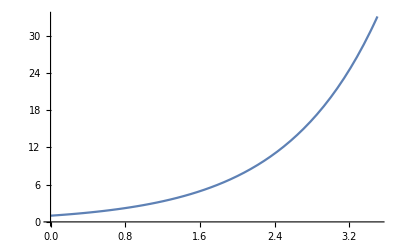

```mathematica
Plot[mainF1[3,{-2,0,2,4,6,8,10},{1/ⅇ^2,1,ⅇ^2,ⅇ^4,ⅇ^6,ⅇ^8,ⅇ^10}],{x1,0,3.5}]
```

```mathematica
Plot[ⅇ^x,{x,0,3.5}]
```

-Graphics-

Тест №2

```mathematica
f[x_]:=ⅇ^x+x^3
```

```mathematica
f/@{-7,-4,-2,0,2,4,7}
```

{-343+1/ⅇ^7,-64+1/ⅇ^4,-8+1/ⅇ^2,1,8+ⅇ^2,64+ⅇ^4,343+ⅇ^7}

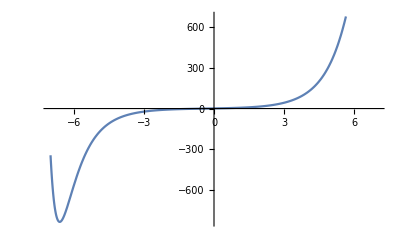

```mathematica
Plot[mainF1[3,{-7,-4,-2,0,2,4,7},{-343+1/ⅇ^7,-64+1/ⅇ^4,-8+1/ⅇ^2,1,8+ⅇ^2,64+ⅇ^4,343+ⅇ^7}],{x1,-7,7}]
```

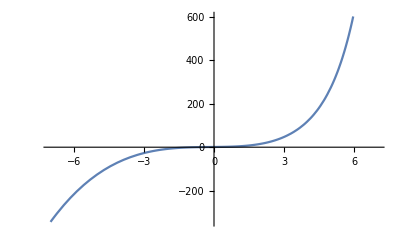

```mathematica
Plot[ⅇ^x+x^3,{x,-7,7}]
```